```mathematica
(*Find Sin(x)+x if x is a zero of the Given  eq.*)
Sin[x]+x/.Solve[2x^2-3x+1==0][[1]]
```

1/2+Sin[1/2]

```mathematica
" OR "
```

```mathematica
a=Solve[2x^2-3x+1==0];
Sin[x]+x/.a[[1]]
```

1/2+Sin[1/2]

```mathematica
(*Calculate the Range(Always +ve,Horizontal distance where   Y_component is zero.) of a projectile *)
(*if Th>90 then Cos will be -ve But Range Always remain +ve( so take Abs[vi t Cos[th]])*)
Simplify[Abs[vi t Cos[th]]/.Solve[vi t Sin[th]-1/2g t^2==0,t][[2]],th>0]
```

2 Abs[(vi^2 Cos[th] Sin[th])/g]

```mathematica
o=Solve[vi t Sin[th]-1/2g t^2==0,t];
vi t Cos[th]/.o[[2]]//Simplify
```

(vi^2 Sin[2 th])/g

```mathematica
(vi^2 Sin[2 th])/g(*Answer.*)
```

```mathematica
(*so far*)f[x_]:=one command
```

```mathematica
(*Subprogramme*)f[x_]:=(command1;command2;command3)
```

```mathematica
(*Write a sub programme to Calculate the Range of a projectile as a function of vi and th and call it for vi=4.5 and arbitrary th . Then call it for vi=2 and th_i=0,Pi/8,,,Pi*)
R[vi_,th_]:=(vi t Cos[th]/.Solve[vi t Sin[th]-1/2g t^2==0,t][[2]]);
R[4.5,th]
"For the List of Angles"
Table[R[2,th],{th,0,Pi,Pi/8}]//N
```

(40.5 Cos[th] Sin[th])/g

For the List of Angles

{0.,2.82843/g,4./g,2.82843/g,0.,-2.82843/g,-4./g,-2.82843/g,0.}

```mathematica
(* Lecture 6 *)
(* Graph(numaricle command.) a sol.of x^2+y^2=4 for -2=<x≥2*)
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
a=.
```

-√(4-x^2)

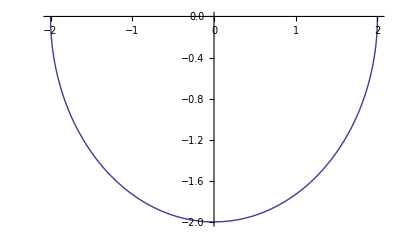

```mathematica
a=Solve[x^2+y^2==4,y];
b=y/.a[[1]]
Plot[b,{x,-2,2}]
```

```mathematica
(*if u r asked to re_do the shift_enter then use the different symbol before =y/. *)
```

```mathematica
(*For two capacitors if Ceq=2.3 micro F for series, Ceq=0.5micro F  for Parallel. Find both capacitences.*)
```

```mathematica
Solve[{c1+c2==0.5 10^-6,1/c1+1/c2==1/(2.3 10^-6)},{c1,c2}]
```

{{c1→2.5×10^-7-1.04283×10^-6 ⅈ,c2→2.5×10^-7+1.04283×10^-6 ⅈ},{c1→2.5×10^-7+1.04283×10^-6 ⅈ,c2→2.5×10^-7-1.04283×10^-6 ⅈ}}

```mathematica
(* Lecture 7 *)
```

```mathematica
Solve[2x^5+6x^3+2x^2+9x+7==0,x]//N
```

{{x→-0.657244},{x→-0.40514-1.42512 ⅈ},{x→-0.40514+1.42512 ⅈ},{x→0.733763-1.37389 ⅈ},{x→0.733763+1.37389 ⅈ}}

```mathematica
(* Solve will return nothing if we can not solve an eq by some formula.
where ANti_derivative fails then Simpson's ,Trapezoidal rules are available. ===========      Numaricle method can always give u Only ONE solution.
Numaricle method will return sol. that is near to the given intitial point. ZERO METHOD: U can find Root by Drawing a graph of The given eq. ============*)
```

```mathematica
Solve[Sin[x]==x,x](* Sin[x]-x *)
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Sin[x]==x,x]

```mathematica
?Solve
```

Solve[eqns,vars] attempts to solve an equation or set of equations for the variables vars. 
Solve[eqns,vars,elims] attempts to solve the equations for vars, eliminating the variables elims.

```mathematica
(*    FindRoot: is a numaricle command. *)
```

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

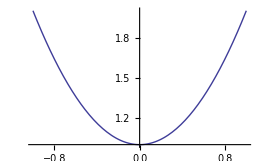

```mathematica
Plot[x^2+1,{x,-1,1}](*has root imaginary={iota,-iota} *)
```

```mathematica
(*FindRoot[2-3x+x^2+0.01*Exp[-Sqrt[Sin[x]]],{x,x0}]*)
```

```mathematica
(*{x->1.004007258824167}*)
```

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
(* Find the equilibrium position of the particle under the 2-3x+x^2+0.01***   ,if it starts from  an equilibrium under 2-3x+x^2=0 *)
```

```mathematica
x0=x/.Solve[2-3x+x^2==0][[1]];(*Perfect Ans.*)
x/.FindRoot[2-3x+x^2+0.01*Exp[-Sqrt[Sin[x]]],{x,x0}]
```

1.00401